# Newton’s Method

For a function g[t], with two roots, can we numerically find the roots from any nearby starting point?

Function[t,t^2-3]

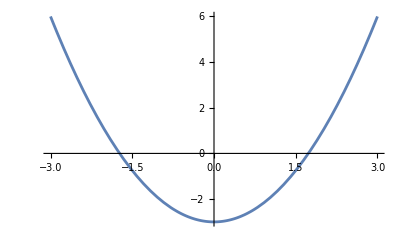

```mathematica
g=t↦t^2-3
Plot[g[t],{t,-3,3}]
```

```mathematica
Solve[g[t]==0,t]
%//N
```

{{t→-√3},{t→√3}}

{{t→-1.73205},{t→1.73205}}

## Newton’s method as a higher order function

```mathematica
newtonStep=f↦tn↦N[tn-f[tn]/f'[tn]]
newton={f,tol}↦t0↦NestWhile[newtonStep[f],t0,t↦Abs[f[t]]>tol]
```

Function[f,Function[tn,N[tn-f[tn]/f'[tn]]]]

Function[{f,tol},Function[t0,NestWhile[newtonStep[f],t0,Function[t,Abs[f[t]]>tol]]]]

```mathematica
NestWhile[newtonStep[g],-1.,t↦Abs[g[t]]>10^-10]
```

-1.73205

```mathematica
newton[g,10^-10][-1]
```

-1.73205

-Graphics-

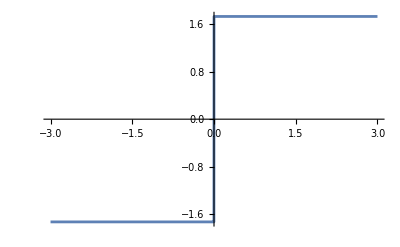

```mathematica
Plot[g[t],{t,-3,3}]
newton[g,10^-4];
Plot[%[t],{t,-3,3}]
```

## Newton Fractals

### Solve for a cubic, with three real roots

-t+t^3

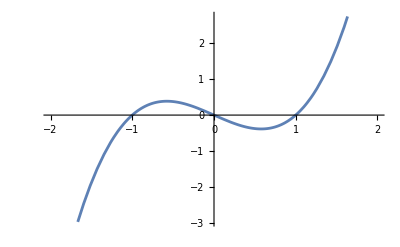

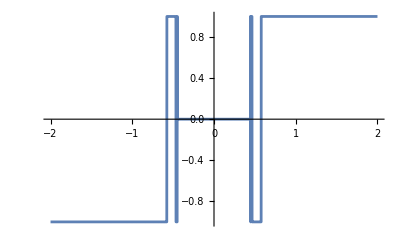

```mathematica
t^3-t
Plot[%,{t,-2,2}]
newton[t↦t^3-t,10^-4];
Plot[%[t],{t,-2,2}]
```

### In the Complex Plane

```mathematica
newton[t↦t^3-t,10^-4];
DensityPlot[Re[%[s+I r]],{s,-2,2},{r,-2,2},PlotPoints->200,PlotRange->{{-2,2},{-2,2},{-2,2}}]
```

-Graphics-

```mathematica
newton[t↦t^3-1,10^-4];
DensityPlot[Arg[%[s+I r]],{s,-2,2},{r,-2,2},PlotPoints->200,PlotRange->{{-2,2},{-2,2},{-π,π}}]
```

-Graphics-

## Higher Order Methods – Householder method

Newton’s method used a linear function, with two parameters, to find an approximation to the nearest zero. We match the parameters with the function value and first derivative.
We can get a higher order method by matching the value, first, and second derivative to a rational function with a single root and one pole.
This is the second order householder method (the first order method is Newton’s method).
This is all an aside for dynamic systems where the first derivative is given, but the second isn’t.

```mathematica
α(t-tz)/(t-tp)
Solve[{
(%/.t->t0)==f0,
(D[%,t]/.t->t0)==f1,
(D[%,{t,2}]/.t->t0)==f2
},{tz,α,tp}]//FullSimplify
tz/.%[[1]]
```

((t-tz) α)/(t-tp)

{{tz→(2 f0 f1)/(-2 f1^2+f0 f2)+t0,α→f0-(2 f1^2)/f2,tp→(2 f1)/f2+t0}}

(2 f0 f1)/(-2 f1^2+f0 f2)+t0

```mathematica
householderStep=f↦tn↦N[tn+(2f[tn]f'[tn])/(-2 f'[tn]^2+f[tn]f''[tn])];
householder={f,tol}↦t0↦NestWhile[householderStep[f],t0,t↦Abs[f[t]]>tol];
```

### Householder fractal

At the cost of requiring the evaluation of a second derivative, we can get a less extreme fractal as the basin of attraction of the roots.

```mathematica
householder[t↦t^3-1,10^-4];
DensityPlot[Arg[%[s+I r]],{s,-2,2},{r,-2,2},PlotPoints->200,PlotRange->{{-2,2},{-2,2},{-π,π}}]
```

-Graphics-